```mathematica
(*反時計まわりが正か負か，人によってことなる．
反時計回りが正のことが多いようなので，ここでもそのように決める*)
Clear["Global`*"];
```

```mathematica
(*回転について*)
Rx[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}}
Ry[t_]:={{Cos[t],0,-Sin[t]},{0,1,0},{Sin[t],0,Cos[t]}}
Rz[t_]:={{Cos[t],Sin[t],0},{-Sin[t],Cos[t],0},{0,0,1}}
```

```mathematica
(*z->x->zオイラー角*)
Dot[Rz[t3],Dot[Rx[t2],Rz[t1]]]//MatrixForm
(*ヨー->ピッチ->ロール角*)
Dot[Rx[t3],Dot[Ry[t2],Rz[t1]]]//MatrixForm
```

(Cos[t1] Cos[t3]-Cos[t2] Sin[t1] Sin[t3] | Cos[t3] Sin[t1]+Cos[t1] Cos[t2] Sin[t3] | Sin[t2] Sin[t3]
-Cos[t2] Cos[t3] Sin[t1]-Cos[t1] Sin[t3] | Cos[t1] Cos[t2] Cos[t3]-Sin[t1] Sin[t3] | Cos[t3] Sin[t2]
Sin[t1] Sin[t2] | -Cos[t1] Sin[t2] | Cos[t2])

(Cos[t1] Cos[t2] | Cos[t2] Sin[t1] | -Sin[t2]
-Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t3]+Sin[t1] Sin[t2] Sin[t3] | Cos[t2] Sin[t3]
Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3] | Cos[t3] Sin[t1] Sin[t2]-Cos[t1] Sin[t3] | Cos[t2] Cos[t3])

```mathematica
(*オイラー角*)
Dot[Rz[γ],Dot[Rx[β],Rz[α]]]//MatrixForm
(*ヨーピッチロール角*)
Dot[Rx[ϕ],Dot[Ry[θ],Rz[ψ]]]//MatrixForm
```

Rz[γ].Rx[β].Rz[α]

Rx[ϕ].Ry[θ].Rz[ψ]

### 回転行列

```mathematica
Clear["Global`*"];
Rspace[{a_,b_,c_,d_}]:=Module[{ind,s,a2,b2,c2,d2},
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
(*s=1/(a*a+b*b+c*c+d*d);*)
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
s=1;
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
{{a2+b2-c2-d2,2*b*c-2a*d,2b*d+2a*c},
{2b*c+2a*d,a2-b2+c2-d2,2c*d-2a*b},
{2b*d-2a*c,2c*d+2a*b,a2-b2-c2+d2}}
];

(*IDEN ={{1,0,0},{0,1,0},{0,0,1}};
S[{a_,b_,c_,d_}]:=1/Sqrt[(a*a+b*b+c*c+d*d)];
R[{a_,b_,c_,d_}]:=IDEN+R0[{a,b,c,d}]*S[{a,b,c,d}];*)
rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,m^2->m2,a^3->a3,b^3->b3,d^3->d3,c^3->c2,
mc^2->mc2,ms^2->ms2,(a2 + b2 + c2 + d2)->a2b2c2d2,ms2->1-mc2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52};

R[{a_,b_,c_,d_}]:=Rspace[{a,b,c,d}];


Print["空間を回転させる回転行列"]
Print[CForm[Rspace[{a,b,c,d}]/.rep]]
Print["空間を固定しベクトルを回転させる回転行列"]
Print[CForm[Transpose[Rspace[{a,b,c,d}]/.rep]]]
N@R[Normalize@{4,1,2,3}]
RR[{a_,b_,c_,d_}]:=Module[{zeros,r},
zeros=Table[Table[0,{i,0,2,1}],{j,0,2,1}];
r=Rspace[{a,b,c,d}];(*ベクトルを回転する行列*)
Join[Join[r,zeros,2],Join[zeros,r,2]]
]
```

空間を回転させる回転行列

List(List(a2 + b2 - c2 - d2,2*b*c - 2*a*d,2*a*c + 2*b*d),List(2*b*c + 2*a*d,a2 - b2 + c2 - d2,-2*a*b + 2*c*d),List(-2*a*c + 2*b*d,2*a*b + 2*c*d,a2 - b2 - c2 + d2))

空間を固定しベクトルを回転させる回転行列

List(List(a2 + b2 - c2 - d2,2*b*c + 2*a*d,-2*a*c + 2*b*d),List(2*b*c - 2*a*d,a2 - b2 + c2 - d2,2*a*b + 2*c*d),List(2*a*c + 2*b*d,-2*a*b + 2*c*d,a2 - b2 - c2 + d2))

{{0.133333,-0.666667,0.733333},{0.933333,0.333333,0.133333},{-0.333333,0.666667,0.666667}}

### 姿勢の計算１

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
(*m=mz/Sqrt[mx^2+my^2]*)
(*n=Norm[{mh,mv}]*)
(*theta=N[-54Degree]*)
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mc,0,ms};
(*{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={0,0,-1,1,0,0};*)
{u[0],u[1],u[2],u[3],u[4],u[5]}={u0,u1,u2,u3,u4,u5};(*sensor value*)
RR[{a,b,c,d}]//MatrixForm
Dimensions[%]
f[{a_,b_,c_,d_}]=Sum[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]/4(*+(1-Sqrt[a^2+b^2+c^2+d^2])*);

F[{a_,b_,c_,d_}]=Simplify@{
D[f[{A,b,c,d}],A]/.{A->a},
D[f[{a,B,c,d}],B]/.{B->b},
D[f[{a,b,C,d}],C]/.{C->c},
D[f[{a,b,c,dd}],dd]/.{dd->d}
};

DF[{a_,b_,c_,d_}]=Simplify[{
D[F[{A,b,c,d}],A]/.{A->a},
D[F[{a,B,c,d}],B]/.{B->b},
D[F[{a,b,C,d}],C]/.{C->c},
D[F[{a,b,c,dd}],dd]/.{dd->d}}]
```

空間を回転させる回転行列

List(List(a2 + b2 - c2 - d2,2*b*c - 2*a*d,2*a*c + 2*b*d),List(2*b*c + 2*a*d,a2 - b2 + c2 - d2,-2*a*b + 2*c*d),List(-2*a*c + 2*b*d,2*a*b + 2*c*d,a2 - b2 - c2 + d2))

空間を固定しベクトルを回転させる回転行列

List(List(a2 + b2 - c2 - d2,2*b*c + 2*a*d,-2*a*c + 2*b*d),List(2*b*c - 2*a*d,a2 - b2 + c2 - d2,2*a*b + 2*c*d),List(2*a*c + 2*b*d,-2*a*b + 2*c*d,a2 - b2 - c2 + d2))

{{0.133333,-0.666667,0.733333},{0.933333,0.333333,0.133333},{-0.333333,0.666667,0.666667}}

(a^2+b^2-c^2-d^2 | 2 b c-2 a d | 2 a c+2 b d | 0 | 0 | 0
2 b c+2 a d | a^2-b^2+c^2-d^2 | -2 a b+2 c d | 0 | 0 | 0
-2 a c+2 b d | 2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c-2 a d | 2 a c+2 b d
0 | 0 | 0 | 2 b c+2 a d | a^2-b^2+c^2-d^2 | -2 a b+2 c d
0 | 0 | 0 | -2 a c+2 b d | 2 a b+2 c d | a^2-b^2-c^2+d^2)

{6,6}

{{d^2 gx0^2+d^2 gy0^2+d^2 gz0^2+d^2 mc^2+d^2 ms^2+3 a^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+b^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+c^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gx0 u0-gy0 u1-gz0 u2-mc u3-ms u5,2 a b (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+gz0 u1-gy0 u2+ms u4,2 a c (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gz0 u0+gx0 u2-ms u3+mc u5,2 a d (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+gy0 u0-gx0 u1-mc u4},{2 a b (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+gz0 u1-gy0 u2+ms u4,a^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+3 b^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+c^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+d^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gx0 u0+gy0 u1+gz0 u2-mc u3+ms u5,2 b c (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gy0 u0-gx0 u1-mc u4,2 b d (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gz0 u0-gx0 u2-ms u3-mc u5},{2 a c (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gz0 u0+gx0 u2-ms u3+mc u5,2 b c (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gy0 u0-gx0 u1-mc u4,3 c^2 gx0^2+d^2 gx0^2+3 c^2 gy0^2+d^2 gy0^2+3 c^2 gz0^2+d^2 gz0^2+3 c^2 mc^2+d^2 mc^2+3 c^2 ms^2+d^2 ms^2+a^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+b^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+gx0 u0-gy0 u1+gz0 u2+mc u3+ms u5,2 c d (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gz0 u1-gy0 u2-ms u4},{2 a d (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+gy0 u0-gx0 u1-mc u4,2 b d (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gz0 u0-gx0 u2-ms u3-mc u5,2 c d (gx0^2+gy0^2+gz0^2+mc^2+ms^2)-gz0 u1-gy0 u2-ms u4,c^2 gx0^2+3 d^2 gx0^2+c^2 gy0^2+3 d^2 gy0^2+c^2 gz0^2+3 d^2 gz0^2+c^2 mc^2+3 d^2 mc^2+c^2 ms^2+3 d^2 ms^2+a^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+b^2 (gx0^2+gy0^2+gz0^2+mc^2+ms^2)+gx0 u0+gy0 u1-gz0 u2+mc u3-ms u5}}

```mathematica
(*確認*)
CForm[R[{a,b,c,d}]/.rep]
```

List(List(a2 + b2 - c2 - d2,2*b*c - 2*a*d,2*a*c + 2*b*d),List(2*b*c + 2*a*d,a2 - b2 + c2 - d2,-2*a*b + 2*c*d),List(-2*a*c + 2*b*d,2*a*b + 2*c*d,a2 - b2 - c2 + d2))

```mathematica
tmp=Collect[F[{a,b,c,d}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep/.rep/.{gx0->0,gy0->0,gz0->-1};;
Variables@tmp
Table[CForm[tmp[[i]]],{i,1,Length[tmp],1}]
```

{a,a2b2c2d2,b,c,d,mc,ms,u0,u1,u2,u3,u4,u5}

{2*a*a2b2c2d2 + c*u0 - b*u1 + a*u2 + (-(a*mc) - c*ms)*u3 + (-(d*mc) + b*ms)*u4 + (c*mc - a*ms)*u5,2*a2b2c2d2*b + d*u0 - a*u1 - b*u2 + (-(b*mc) - d*ms)*u3 + (-(c*mc) + a*ms)*u4 + (-(d*mc) + b*ms)*u5,2*a2b2c2d2*c + a*u0 + d*u1 - c*u2 + (c*mc - a*ms)*u3 + (-(b*mc) - d*ms)*u4 + (a*mc + c*ms)*u5,2*a2b2c2d2*d + b*u0 + c*u1 + d*u2 + (d*mc - b*ms)*u3 + (-(a*mc) - c*ms)*u4 + (-(b*mc) - d*ms)*u5}

```mathematica
tmp=Collect[DF[{a,b,c,d}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep/.{gx0->0,gy0->0,gz0->-1};
Variables@tmp
Do[Print@CForm[FullSimplify[tmp[[i]]]],{i,1,Length[tmp],1}]
```

{a,a2,b,b2,c,c2,d,d2,mc,ms,u0,u1,u2,u3,u4,u5}

List(2*(3*a2 + b2 + c2 + d2) + u2 - mc*u3 - ms*u5,4*a*b - u1 + ms*u4,4*a*c + u0 - ms*u3 + mc*u5,4*a*d - mc*u4)

List(4*a*b - u1 + ms*u4,2*(a2 + 3*b2 + c2 + d2) - u2 - mc*u3 + ms*u5,4*b*c - mc*u4,4*b*d + u0 - ms*u3 - mc*u5)

List(4*a*c + u0 - ms*u3 + mc*u5,4*b*c - mc*u4,2*(a2 + b2 + 3*c2 + d2) - u2 + mc*u3 + ms*u5,4*c*d + u1 - ms*u4)

List(4*a*d - mc*u4,4*b*d + u0 - ms*u3 - mc*u5,4*c*d + u1 - ms*u4,2*(a2 + b2 + c2 + 3*d2) + u2 + mc*u3 - ms*u5)

{-0.559193,0.,-0.829038}

{u0→-0.939693,u1→0.,u2→-0.34202,u3→-0.559193,u4→0.,u5→-0.829038}

70.度となるはず

General::munfl: (2.03035×10^-115)^3は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: (4.06071×10^-115)^3は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

1.

{0.819152,7.89683×10^-177,0.573576,1.57937×10^-176}

General::munfl: 1.57937×10^-176 1.57937×10^-176は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 7.89683×10^-177 7.89683×10^-177は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 7.89683×10^-177 1.57937×10^-176は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

{5.85215×10^-174,5.20241×10^-174,70.,70.}

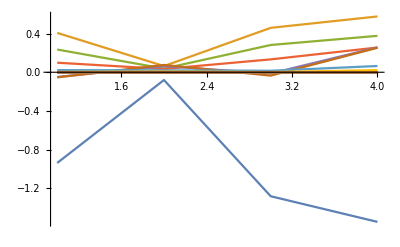

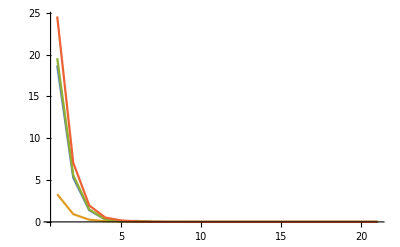

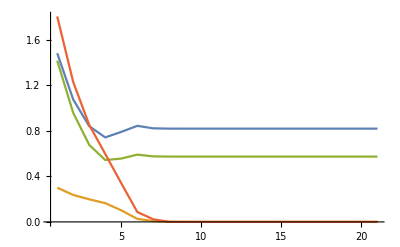

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]


θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};
mc=Cos[θ];
ms=Sin[θ];

(*センサーの値を模擬*)
dθ=70/180.*Pi;
rot=Rspace[{Cos[dθ/2],0,Sin[dθ/2],0}];
A=Dot[rot,{0,0,-1}];
M=Dot[rot,{mc,0,ms}]
rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}
Print[N[dθ]/Pi*180,"度となるはず"];


data={};
abcd={};
dq={1,0,0,0};
DQ={};

{a,b,c,d}={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
Do[
If[Mod[i,1],
{a,b,c,d}=Normalize[{a,b,c,d}];
];
(*{a,b,c,d}=Normalize[{a,b,c,d}];*)
dq=(Dot[Inverse[DF[{a,b,c,d}]/.rep],F[{a,b,c,d}]/.rep]);
{a,b,c,d}-=dq;
AppendTo[data,F[{a,b,c,d}]/.rep];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d}/.rep];
,{i,0,20,1}];
Norm[{a,b,c,d}]
{a,b,c,d}=Normalize[{a,b,c,d}]
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}],2ArcTan[Norm[{b,c,d}]/a]}/Pi*180
ListPlot[DQ,Joined->True,PlotRange->All]
ListPlot[Transpose@data,Joined->True,PlotRange->All]
ListPlot[Transpose@abcd,Joined->True,PlotRange->All]
```

```mathematica
(*.08加速度をいっぺんに計算する*)
```

### 姿勢の計算２

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mc,0,ms};
{V0[0],V0[1],V0[2],V0[3],V0[4],V0[5]}={gx0+dAx,gy0+dAy,gz0+dAz,mc,0,ms};
{vs[0],vs[1],vs[2],vs[3],vs[4],vs[5]}={u0,u1,u2,u3,u4,u5};(*sensor value*)
RR[{a,b,c,d}]//MatrixForm
Dimensions[%]
(*f[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]+Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*V0[j],{j,0,5,1}])^2,{i,0,5,1}];
*)

f[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*V0[j],{j,0,5,1}])^2,{i,0,5,1}]+Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}];


F[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Simplify@{
D[f[{A,b,c,d},{dAx,dAy,dAz}],A]/.{A->a},
D[f[{a,B,c,d},{dAx,dAy,dAz}],B]/.{B->b},
D[f[{a,b,C,d},{dAx,dAy,dAz}],C]/.{C->c},
D[f[{a,b,c,dd},{dAx,dAy,dAz}],dd]/.{dd->d},
D[f[{a,b,c,d},{X,dAy,dAz}],X]/.{X->dAx},
D[f[{a,b,c,d},{dAx,X,dAz}],X]/.{X->dAy},
D[f[{a,b,c,d},{dAx,dAy,X}],X]/.{X->dAz}
};

DF[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Simplify[{
D[F[{A,b,c,d},{dAx,dAy,dAz}],A]/.{A->a},
D[F[{a,B,c,d},{dAx,dAy,dAz}],B]/.{B->b},
D[F[{a,b,C,d},{dAx,dAy,dAz}],C]/.{C->c},
D[F[{a,b,c,dd},{dAx,dAy,dAz}],dd]/.{dd->d},
D[F[{a,b,c,d},{X,dAy,dAz}],X]/.{X->dAx},
D[F[{a,b,c,d},{dAx,X,dAz}],X]/.{X->dAy},
D[F[{a,b,c,d},{dAx,dAy,X}],X]/.{X->dAz}
}];

rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,m^2->m2,a^3->a3,b^3->b3,d^3->d3,c^3->c2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52};
```

(a^2+b^2-c^2-d^2 | 2 b c-2 a d | 2 a c+2 b d | 0 | 0 | 0
2 b c+2 a d | a^2-b^2+c^2-d^2 | -2 a b+2 c d | 0 | 0 | 0
-2 a c+2 b d | 2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c-2 a d | 2 a c+2 b d
0 | 0 | 0 | 2 b c+2 a d | a^2-b^2+c^2-d^2 | -2 a b+2 c d
0 | 0 | 0 | -2 a c+2 b d | 2 a b+2 c d | a^2-b^2-c^2+d^2)

{6,6}

{u0→0.318756,u1→0.,u2→-1.07163,u3→0.438371,u4→0.,u5→-0.898794}

10.度となるはず

{-0.0264353,0.,-0.00972306,0.,-0.356448,0.,0.0163499}

{0.0189136,0.,0.00454235,0.,0.0288626,0.,0.0352544}

{0.000656729,0.,0.000454986,0.,0.00325081,0.,0.00243976}

{2.78354×10^-6,0.,1.36191×10^-6,0.,9.82708×10^-6,0.,0.000010023}

{3.51244×10^-11,0.,1.7911×10^-11,0.,1.29763×10^-10,0.,1.47692×10^-10}

{-6.63405×10^-17,0.,-1.68696×10^-18,0.,-2.08999×10^-17,0.,2.92287×10^-16}

{-2.50328×10^-16,0.,6.88317×10^-18,0.,1.13977×10^-16,0.,-3.02809×10^-16}

{1.07857×10^-16,0.,-5.66336×10^-18,0.,-8.23826×10^-17,0.,5.74569×10^-18}

{1.05525×10^-16,0.,-4.9195×10^-19,0.,-2.785×10^-17,0.,4.2535×10^-18}

{1.02634×10^-16,0.,-8.36156×10^-18,0.,9.91111×10^-18,0.,-6.93787×10^-18}

{1.0366×10^-16,0.,3.37007×10^-19,0.,8.85977×10^-18,0.,8.96091×10^-19}

{1.0366×10^-16,0.,3.37007×10^-19,0.,8.85977×10^-18,0.,8.96091×10^-19}

{1.0366×10^-16,0.,3.37007×10^-19,0.,8.85977×10^-18,0.,8.96091×10^-19}

«8 more identical outputs»

1.00687

Ax,Ay,Az={0.329298,0.,-0.0517118}

YPR={0.,0.,0.545095,0.537678}

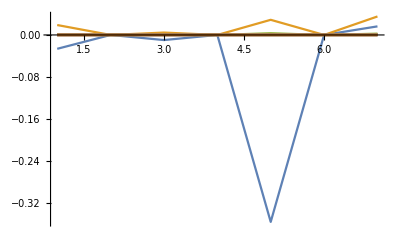

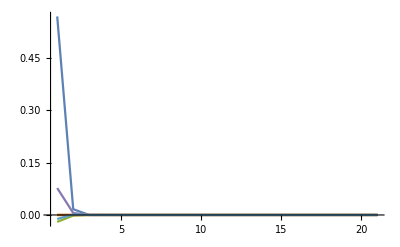

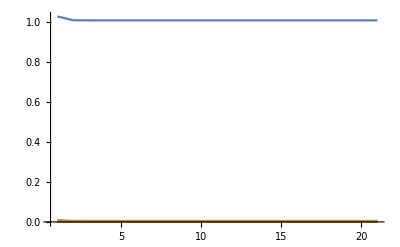

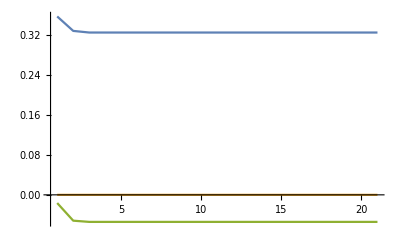

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]
θ=-54/180*Pi;
(*基準となる姿勢における値，物体の加速度成分を除いたもの*)
{gx0,gy0,gz0}={0,0,-1};
mc=Cos[θ];
ms=Sin[θ];

dθ=10/180.*Pi;
(*センサーの値，テスト値*)
axis=Normalize@{0.,1,0.};
rot=Rspace[{Cos[dθ/2],axis[[1]]Sin[dθ/2],axis[[2]]Sin[dθ/2],axis[[3]]Sin[dθ/2]}];
A=Dot[rot,{gx0,gy0,gz0}+{.5,0.,0.}];
M=Dot[rot,{mc,0,ms}];
rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}


Print[N[dθ]/Pi*180,"度となるはず"];
data={};
abcd={};
DQ={};
Axyz={};

{Ax,Ay,Az}={0,0,0};
{a,b,c,d}=Normalize@{1,0,0,0};
Do[
(*If[Mod[i,1],
{a,b,c,d}=Normalize[{a,b,c,d}];
];
{a,b,c,d}=Normalize[{a,b,c,d}];
*)(* {Ax,Ay,Az}={0,0,0};*)
dq=(Dot[Inverse[DF[{a,b,c,d},{Ax,Ay,Az}]/.rep],F[{a,b,c,d},{Ax,Ay,Az}]/.rep]);
Print[dq];
{a,b,c,d,Ax,Ay,Az}-=dq;
AppendTo[data,F[{a,b,c,d},{Ax,Ay,Az}]/.rep];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d}/.rep];
AppendTo[Axyz,{Ax,Ay,Az}/.rep];
,{i,0,20,1}];
Norm[{a,b,c,d}]
(*{a,b,c,d}=Normalize[{a,b,c,d}]*)
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
(*Print["Ax,Ay,Az=",{Ax,Ay,Az}]*)
Print["Ax,Ay,Az=",Dot[Transpose@Rspace[{a,b,c,d}],{Ax,Ay,Az}]]
Print["YPR=",{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}],2ArcTan[Norm[{b,c,d}]/a]}/Pi*180.]
ListPlot[DQ,Joined->True,PlotRange->All]
ListPlot[Transpose@data,Joined->True,PlotRange->All]
ListPlot[Transpose@abcd,Joined->True,PlotRange->All]
ListPlot[Transpose@Axyz,Joined->True,PlotRange->All]
```

```mathematica
Subdivide[0,10,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
{1(*ms*),-90}
{2(*ms*),90}
```

```mathematica
freq=50
N[1/freq*1000](*Hz*)
```

50

20.

```mathematica
p=180
(650.-150.)*p/180.+150
```

180

650.

```mathematica
N[4096*150/20]
N[4096*500/20]
```

```mathematica
1/20.*20
```

1.

```mathematica
1/50.*100
```

2.

```mathematica
0.4==1/frew*4096
0.4==1/frew*4096
```

```mathematica
frew==4096/2.4
frew==4096/0.4
```

frew==1706.67

frew==10240.

```mathematica
frew==4096/1.0
```

frew==4096.

```mathematica
hs=50
Solve[pulse*((1/hs)/2^12)(*sec*)==0.0004,pulse]
Solve[pulse*((1/hs)/2^12)(*sec*)==0.0024,pulse]
```

50

{{pulse→81.92}}

{{pulse→491.52}}